# Automaty komórkowe

## Wprowadzenie

### Charakteryzacja i definicje

Automaty komórkowe są dyskretnymi modelami rozważanymi między innymi w informatyce, matematyce i fizyce, skłądającymi się z regularnej siatki o skończonym wymiarze, która składa się z komórek, z których każda może być w jednym z określonych stanów (których pula jest skończona).

Dla każdej z komórek definiuje się zbiór jej sąsiadów jako zbiór komórek położonych w określony sposób względem niej.

Dla automatu komórkowego definiujemy stan początkowy poprzez okreslenie stanu kazdej z komórek. Natomiast nowa generacja komórek powstaje poprzez zastosowanie określonej reguły w postaci funkcji matematycznej, która określa nowy stan każdej z komórek an podstawie stanu komórek w jej sąsiedztwie.

### Trochę historii

Automaty komórkowe zostały odkryte w latach 40-tych przez polskiego matematyka Stanisława Ulama oraz  węgierskiego matematyka Johna von Neumann’a.

Dopero jednak a latach 70-tych,  kiedy powstała “Gra w życie”, automaty komórkowe opóściły jedynie środowisko akademickie.

W latach 80-tych do grona badaczy nad automatami komórkowymi dołączył Wolfram (twórca Mathematici), który wraz z Matthew Cook’iem dowiódł kompletności Turiunga tych automatów.

## Pomocne narzędzia

W celu pracy z automatami komórkowymi zdefiniujemy sobie zestaw pomocnych funkcji, dzięki którym będziemy mogli w bardziej zwięzły i przejrzysty sposób obserwować ewolucję automatów.

```mathematica
AnimateAutomata[rule_, init_,steps_, mapPlot_:ArrayPlot]:=
Module[
{automataHistory=CellularAutomaton[rule,init,steps]},
Animate[
mapPlot@automataHistory[[n]],
{n, 1, steps+1, 1},
AnimationRunning->False,
AnimationRepetitions->Infinity
]
];
Print2D=MatrixPlot[#, ColorFunction->"Monochrome",Ticks->None,ImageSize->Tiny, FrameTicks->None]&;
```

## Gra w życie Conway’a

### Opis i zasady

Jest to jeden z pierwszych i bardziej znanych automatów komórkowych, wzbudzający zainteresowanie ze względu na zaskakujący sposób, w jaki potrafią ewoluować struktury na siatce.

Jako sąsiadów komórki w tym automacie definiujemy wszystkie 8 komórek przylegające do danej bokami lub rogami. Każda komórka znajduje się w 1 z 2 stanów - jest “żywa” bądź “martwa”. Komórka martwa rodzi się, wtedy i tylko wtedy gdy ma dokładnie 3 żywych sąsiadów, natomiast komórka żywa pozostaje żywa wtedy i tylko wtedy gdy ma 2 lub 3 żywych sąsiadów, w przypadku innej liczby umiera. W Mathematice regułe tę można zdefiniować w następujący sposób, tak by była prawidłowo interpretowana przez dostępną w Mathematice funkcje CellurarAutomaton

```mathematica
GoLRule=<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->"Moore"|>;
```

Warto zwrócić uwagę, jaki jest sens takiego zapisu tej reguły przejścia automatu komórkowego.

Na początku zależy wyróżnić dwa sposoby uwaluacji generacji komórek: w pierwszej z nich (“TotalisticCode”) bierzemy pod uwagę wszystkie komórki to jest sąsiedzi + komórka ewoluująca, natomiast w drugiej (“OuterTotalisticCode”) pod uwagę bierzemy oddzielnie sąsiadów komórki i daną komórkę przy zliczaniu liczby żywych komórek. Dla przykładu w przypadku 2D w kodowaniu “TotalisticCode” możemy powiedzieć, że komórka będzie żywa, jeżeli w kwadracie 3x3 w poprzedniej generacji 2 komórki były żywe. Natomiast w kodowaniu “OuterTotalisticCode” możemy powiedzieć, że komórka będzie żywa, jeżeli była żywa i 1 z jej sąsiadów był żywy lub była martwa i 2 jej sąsiadów było żywych.

Warto początkowo zwrócić uwagę, jak wygląda definicja reguł dla jednowymiarowego automatu - definiuje się ją bowiem jako liczbę całkowitą z przedziału [0, 255], a więc liczbę 7 bitową. Jest to związane z tym, że dla automatu jednowymiarowego rozważa się stan środkowej komórki na podstawie stanów jej sąsiadów w określonej kolejności i zapisuje się stany komórek po zmianie w systemie dwójkowym. Dla przykładu sławna “zasada 30” badana przez Wolframa, zapisuje się w systemie binarnym jako

```mathematica
IntegerString[30, 2, 7]
```

0011110

co przekłada się na następujące zasady zmiany przy ewolucji generacji komórek automatu (kolejność przejść jest ustalona w Mathematice)

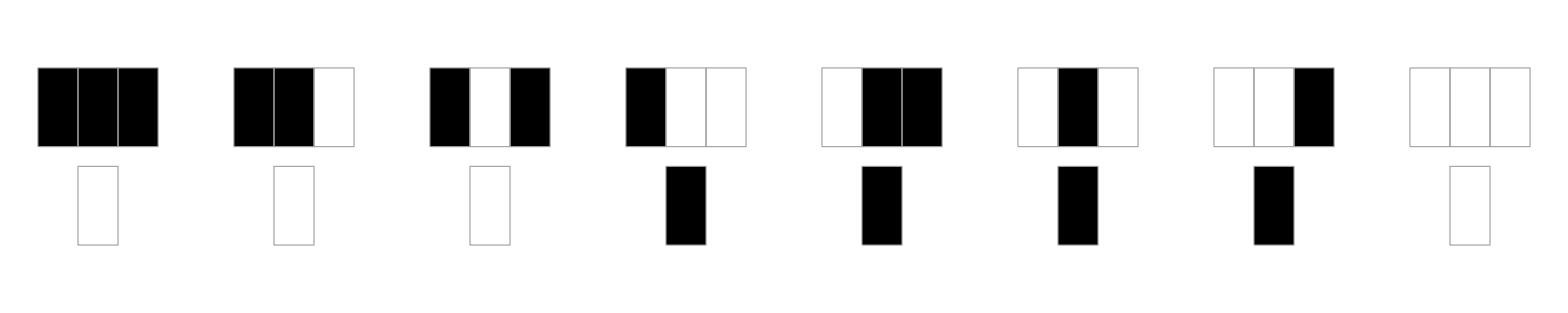

```mathematica
RulePlot@CellularAutomaton[30]
```

jako że przy generowaniu w Mathematice wszystkich uporządkowanych trójek zer i jedynek dostaniemy wynik właśnie z taką kolejnością, a za pomocą 0 i 1 możemy zdefiniować stan komórki środkowej w następnej generacji.

```mathematica
ArrayPlot[{#},Mesh->All, ImageSize->35]&/@Tuples[{1,0},3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Przypadek dwuwymiarowy jest nieco bardziej skomplikowany, co wynika z tego, że wyróżniamy dla niego co najmniej 2 różne typy sąsiedztwa (które zaprezentujemy za pomocą ilustracji).

```mathematica
GridPlotArray[data_]:= MatrixPlot[SparseArray[data, {5, 5}],Mesh->All,Frame->False];
GridPlotArray/@{{
{i_,j_}/;i==j==3->2, 
{i_,j_}/;EuclideanDistance[{3, 3}, {i, j}]≤√2->1}, 
{{i_,j_}/;i==j==3->3, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==1->2, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==2∧EuclideanDistance[{3, 3}, {i, j}]≥2->1}
}//ImageAssemble
```

-Graphics-

Pierwszym z nich jest jest sąsiedztwo Moore’a, w którym komórka sąsiaduje ze wszystkimi 8 komórkami dookoła siebie. Oprócz tego wyróżniamy również sąsiedztwo von Neumanna, które obejmuje 4 komórki, a w wersji rozszerzonej 8.

Zatem chcąc wyjaśnić znaczenie wyżej zdefiniowanej  zasady gry w życie (GoLRule) potrzebne jest zrozumienie pierwszej jej części - kodu reprezentującego ewaluację komórki do następnej generacji w sąsiedztwie 8 komórek (Moore’a).

```mathematica
IntegerString[224, 2, 18]
```

000000000011100000

Tak więc porównując ten wynik z reprezentacją graficzną zasad “gry w życie” i wiedząc, że komórka w kolejnej generacji jest żywa wtw. gdy miała 3 żywych sąsiadów lub była żywa i miała 2 żywych sąsiadów.

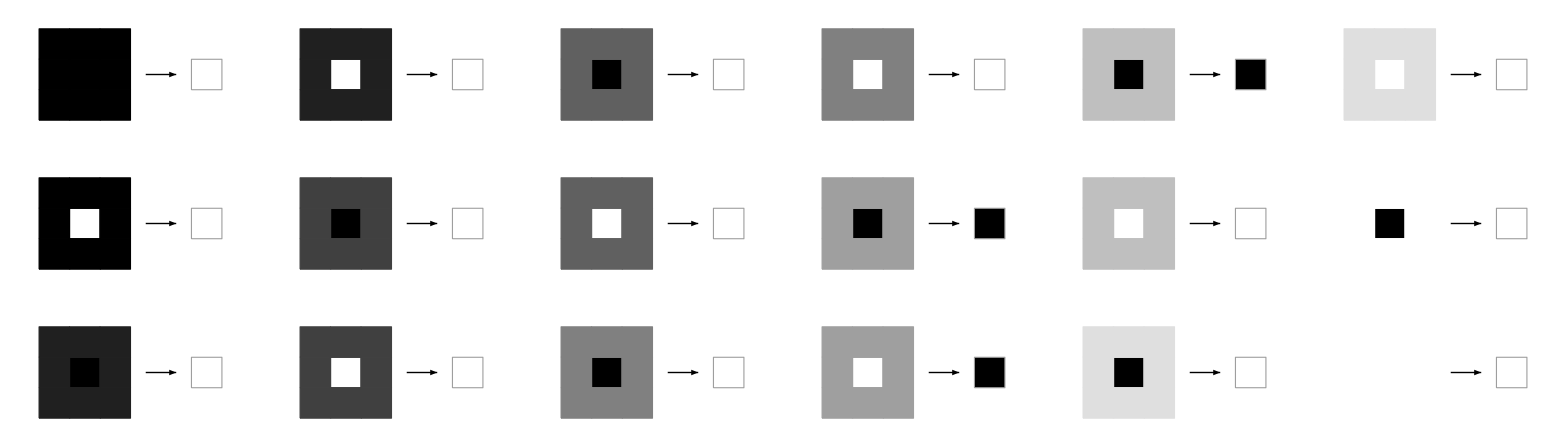

```mathematica
RulePlot[CellularAutomaton[GoLRule]]
```

Widać zatem, że taki zapis zasady ewaluacji komórek za pomocą pojedynczej liczby 18-sto bitowej (jako że stosujemy kodowania “OuterTotalisticRule”) oznacza, dla jakiej liczby sąsiadów komórki komórka środkowa staje się żywa w następnej generacji, gdzie bity liczby odpowiadają kolejnym liczbom żywych sąsiadów komórki (w przypadku sąsiedztwa Moore’a 8, 7, ..., 1, 0, dla kolejno żywej i martwej komórki w poprzedniej generacji).

### Przykłady ewaluacji

Ewolucja automatu komórkowego z przyjęciem zasad gry w życie uwidacznia kilka charakterystycznych typów struktur, które można podzielić w następujący sposób

#### Struktury niezmienne

Przykładami struktur niezmiennych, to jest takich, w których w każdej generacji te same komórki są żywe, są klocek, ul, bochenek, łódź, kadź

```mathematica
block={{1, 1},{1, 1}};
beehive={{0,1,1,0},{1,0,0,1},{0,1,1,0}};
loaf={{0, 1, 1,0},{1, 0, 0, 1},{0, 1, 0, 1},{0, 0, 1, 0}};
boat={{1, 1, 0},{1, 0, 1},{0, 1, 0}};
tub={{0, 1, 0},{1, 0, 1},{0, 1, 0}};
Column[
AnimateAutomata[GoLRule,{#,0},60, Print2D]&/@{block, beehive, loaf, boat, tub}
]
```

#### Oscylatory

Przykładżabka, ami układów oscylujących w “grze w życie” są światła uliczne, żabka, latarnia morska, pulsar i pentadekatlon

```mathematica
blinker={{0,0,0},{1,1,1},{0,0,0}};
toad={{0, 1, 1, 1},{1, 1, 1, 0}};
beacon={{1, 1, 0, 0},{1, 1, 0, 0},{0, 0,1, 1},{0, 0, 1, 1}};
pulsar={
{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}};
pentadecathlon={{1, 1, 1},{1, 0, 1},{1, 1, 1},{1, 1, 1},{1, 1, 1},{1, 1, 1},{1, 0, 1},{1, 1, 1}};
Column[
AnimateAutomata[GoLRule,{#,0},60, Print2D]&/@{blinker, toad, beacon, pulsar, pentadecathlon}
]
```

#### Statki

Wsród statkow można przede wszystkim wyróznić szybowiec oraz statek koszmiczny, które przemieszczają się po planszy gry

```mathematica
glider={{0,1,0},{0,0,1},{1,1,1}};
spaceship={{1, 0, 0, 1, 0},{0, 0, 0, 0, 1},{1, 0, 0, 0, 1},{0, 1, 1, 1,1}};
Column[
AnimateAutomata[GoLRule,{#,0},60, Print2D]&/@{glider, spaceship}
]
```

#### Pozostałe

Ponadto wyróznia się również takie struktury jak działa, które “produkują” nieustannie ładunki (przykładem jest słynny reprezentant gry “Gosper Glider Gun”)

```mathematica
gosperGliderRun={
{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 1},{0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}};
AnimateAutomata[GoLRule,{gosperGliderRun,0},120, Print2D]
```

```mathematica
AnimateAutomata[<|"TotalisticCode"->14,"Dimension"->3,"Neighborhood"->27|>,{{{{1}}},0},20, ArrayMesh]
```